# Electroweak baryogenesis at high wall velocities (arXiv:2001.00568)

## Master Code Reformulated

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;
(*******************************************************************************************************************)
(**********************************************************************************************)
```

```mathematica
(*gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];*)
gtab=Import["./satoshi_dof.dat","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
```

```mathematica
(*params3=Import["SCANS/BAU/Z2_breaking_sols_BAU.csv","Dataset","HeaderLines"->1];*)
```

```mathematica
params3=Import["SCANS/BAU/Z2_breaking_sols_BAU_2.csv","Dataset","HeaderLines"->1];
```

```mathematica
Tnlist=params3[All,"Tnuc_0"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
shighlist=params3[All,"shigh"];
slowlist=params3[All,"slow"];
alphalist=params3[All,"alpha_max"];
(*alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];*)
```

```mathematica
MasterFunction[Tn_,vw_,h0_,Lh_,sl_,sh_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,sl,sh,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
(*s[z_]:=s0/2(1-Tanh[z/Ls-ds]);*)(**equation (50)**)
s[z_]:=(sl-sh)/2 Tanh[z/Ls-ds]+(sl+sh)/2;
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];
```

```mathematica
(*MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_l=",slowlist[[i]]," s_h=",shighlist[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
```

```mathematica
MasterPars[-1]
```

Pars α=0.0144215 T_n=96.4894 v_w=0.548567 T_p=101.599 v_p=0.478516 h_0=209.756 L_h=0.170973 s_l=-208.144 s_h=-237.352 L_s=0.170973 ds=0.372552

```mathematica
(*MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
(*MasterOutputVelOld[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];*)
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,7,points];
```

```mathematica
ΛCP=params3[All,"Lam_CP"][[-10]]
```

128.403

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 92714.8 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

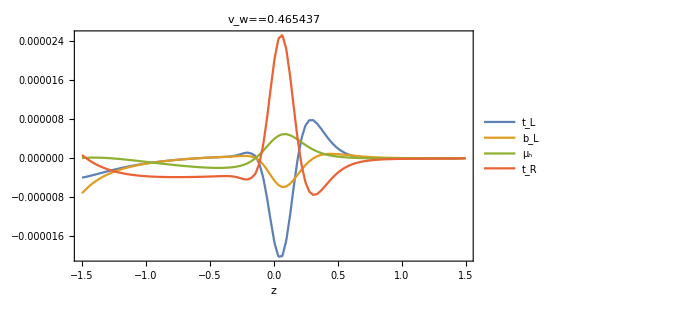
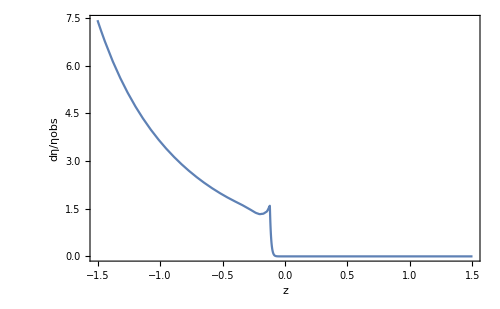
{-Graphics-,-Graphics-,4.56714}

```mathematica
MasterOutputVel[-10,ΛCP,100]
```

```mathematica
BAUscale[i_]:=Module[{BAU,res,numpoints=100},

BAU[Λ_?NumericQ]:=BAU[Λ?NumericQ]=MasterOutputVel[i,Λ,numpoints][[3]];

If[BAU[100]<1,Print[Show[MasterOutputVel[i,100,numpoints][[1]]]];Print["Did not work!!, \n Λ_CP="];Return[99]];

Quiet[
res=Λ/.FindRoot[BAU[Λ]-1,{Λ,100,1000},AccuracyGoal->2,PrecisionGoal->2(*,EvaluationMonitor:>Print["Λ=",Λ," BAU=",BAU[Λ]]*)];
];

MasterPars[i];
Print["Λ=",res];
Print[MasterOutputVel[i,res,numpoints][[1]]];
Return[res]
];
```

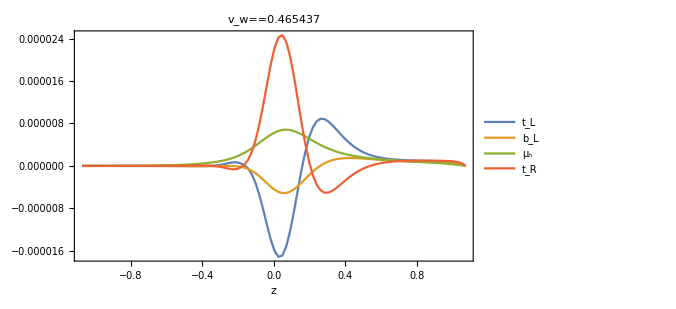

Did not work!!, 
 Λ_CP=

99

```mathematica
BAUscale[-10]
```

```mathematica
BAULambda80=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["SCANS/BAU/BAU_3.csv",BAULambda80]
```

Pars α=0.00619627 T =113.919 v =0.417936 T =114.769 v =0.405126 h =180.659 L =
                   n          w           p          p           0          h
 
>   0.20348 s =212.159 s =232.561 L =0.20348 ds=0.442151
             l          h          s

Λ=106.606

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

«5 more identical outputs»

11
NDSolve::berr: The scaled boundary value residual error of 1.35929 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

9
NDSolve::berr: The scaled boundary value residual error of 1.58148 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

6
NDSolve::berr: The scaled boundary value residual error of 1.44465 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 83476.3
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

7
NDSolve::berr: The scaled boundary value residual error of 7.11034 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 1141.86
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

6
NDSolve::berr: The scaled boundary value residual error of 9.14479 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

9
NDSolve::berr: The scaled boundary value residual error of 2.50396 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

7
NDSolve::berr: The scaled boundary value residual error of 2.46493 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

6
NDSolve::berr: The scaled boundary value residual error of 3.29409 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 2867.87
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 13488.5
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 16213.3
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00894646 T =106.94 v =0.512205 T =109.671 v =0.476356 h =194.354 L =
                   n         w           p          p           0          h
 
>   0.199099 s =-216.54 s =-240.105 L =0.199099 ds=0.402242
              l          h           s

Λ=121.058

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 74978.3
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00404872 T =121.28 v =0.311169 T =121.539 v =0.306413 h =158.539 L =
                   n         w           p          p           0          h
 
>   0.226211 s =226.961 s =242.384 L =0.18994 ds=0.531826
              l          h          s

Λ=113.904

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

7
NDSolve::berr: The scaled boundary value residual error of 1.07338 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00297849 T =127.878 v =0.270113 T =128.023 v =0.267265 h =142.412 L =
                   n          w           p          p           0          h
 
>   0.20809 s =265.351 s =281.294 L =0.17507 ds=0.500252
             l          h          s

Λ=101.694

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

General::stop: Further output of NDSolve::bvluc
     will be suppressed during this calculation.

NDSolve::berr: The scaled boundary value residual error of 2.97858
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr
     will be suppressed during this calculation.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 123336.
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 102567.
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.0043633 T =119.902 v =0.33192 T =120.225 v =0.326231 h =162.464 L =
                  n          w          p          p           0          h
 
>   0.238438 s =222.947 s =239.177 L =0.200084 ds=0.536731
              l          h          s

Λ=126.84

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 9671.14
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 9675.45
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00894646 T =106.94 v =0.516437 T =109.805 v =0.479149 h =193.974 L =
                   n         w           p          p           0          h
 
>   0.225984 s =-216.616 s =-240.104 L =0.187534 ds=0.485784
              l           h           s

Λ=159.406

Pars α=0.00238286 T =128.926 v =0.191266 T =128.983 v =0.189789 h =129.541 L =
                   n          w           p          p           0          h
 
>   0.216014 s =290.868 s =300.869 L =0.182266 ds=0.526477
              l          h          s

Λ=105.225

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 18671.9
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

8
NDSolve::berr: The scaled boundary value residual error of 1.20004 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 346965.
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 39335.9
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

6
NDSolve::berr: The scaled boundary value residual error of 1.69029 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00421691 T =120.419 v =0.322502 T =120.71 v =0.317259 h =160.546 L =
                   n          w           p         p           0          h
 
>   0.23754 s =224.113 s =239.516 L =0.199394 ds=0.535742
             l          h          s

Λ=113.27

Pars α=0.00619627 T =113.919 v =0.419886 T =114.784 v =0.406923 h =180.6 L =
                   n          w           p          p           0        h
 
>   0.209335 s =212.171 s =232.561 L =0.174954 ds=0.524912
              l          h          s

Λ=119.127

Pars α=0.00677368 T =112.78 v =0.457559 T =114.077 v =0.439493 h =184.074 L =
                   n         w           p          p           0          h
 
>   0.196261 s =-211.401 s =-231.867 L =0.196261 ds=0.413337
              l           h           s

Λ=113.613

Pars α=0.00620547 T =116.4 v =0.486325 T =118.051 v =0.465437 h =178.088 L =
                   n        w           p          p           0          h
 
>   0.214301 s =209.946 s =236.797 L =0.177405 ds=0.448099
              l          h          s

Λ=128.403

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

8
NDSolve::berr: The scaled boundary value residual error of 3.7859 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00755716 T =109.971 v =0.468108 T =111.513 v =0.446557 h =189.123 L =
                   n          w           p          p           0          h
 
>   0.206432 s =207.745 s =230.24 L =0.206432 ds=0.435205
              l          h         s

Λ=114.036

Pars α=0.0127329 T =99.3181 v =0.535319 T =103.534 v =0.477866 h =206.687 L =
                  n          w           p          p           0          h
 
>   0.170952 s =-205.503 s =-232.756 L =0.170952 ds=0.372868
              l           h           s

Λ=106.823

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

6
NDSolve::berr: The scaled boundary value residual error of 2.21776 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00406956 T =120.358 v =0.288467 T =120.573 v =0.284204 h =158.192 L =
                   n          w           p          p           0          h
 
>   0.231198 s =-214.894 s =-228.591 L =0.194066 ds=0.547398
              l           h           s

Λ=102.469

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

7
NDSolve::berr: The scaled boundary value residual error of 4.28936 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Pars α=0.00262252 T =128.151 v =0.214553 T =128.23 v =0.21269 h =134.705 L =
                   n          w           p         p          0          h
 
>   0.213334 s =295.211 s =306.112 L =0.179936 ds=0.519889
              l          h          s

Λ=102.543

Pars α=0.00342054 T =125.151 v =0.298985 T =125.356 v =0.2952 h =149.119 L =
                   n          w           p          p         0          h
 
>   0.223473 s =281.761 s =295.645 L =0.188045 ds=0.505499
              l          h          s

Λ=128.092

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

General::stop: Further output of NDSolve::bvluc
     will be suppressed during this calculation.

6
NDSolve::berr: The scaled boundary value residual error of 9.14479 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr
     will be suppressed during this calculation.

Pars α=0.0144215 T =96.4894 v =0.548567 T =101.599 v =0.478516 h =209.756 L =
                  n          w           p          p           0          h
 
>   0.170973 s =-208.144 s =-237.352 L =0.170973 ds=0.372552
              l           h           s

Λ=110.815

Pars α=0.00404872 T =121.28 v =0.311169 T =121.539 v =0.306413 h =158.539 L =
                   n         w           p          p           0          h
 
>   0.226211 s =226.961 s =242.384 L =0.18994 ds=0.531826
              l          h          s

Λ=113.904

Pars α=0.0126788 T =99.3838 v =0.534399 T =103.548 v =0.477582 h =206.652 L =
                  n          w           p          p           0          h
 
>   0.173711 s =-211.289 s =-239.171 L =0.173711 ds=0.376529
              l           h           s

Λ=113.451

SCANS/BAU/BAU_2.csv